## Newton — Problem Set 2 — The First Three Lemmas

## Due Friday, Sep. 16 (beginning of class)

## In our readings so far (through Thursday, Sep. 15), Newton (1) defined things such as quantity of motion and quantity of impressed force. Then having made these definitions, he has (2) introduced his Three Laws of Motion, then (3) explained addition of forces and the motion resulting from such addition, (4) defined center of mass and described its motion and argued that forces among the bodies in a system do not alter the motion of the center of mass, and finally, (5) begun computing the area under a curve. This second problem set creates a concrete example for each of these topics.

### 1. Quantity of Motion

A cloud drifts lazily eastward from the Owens Valley toward Deep Springs. Its speed is estimated by you as 5 muff.

After crossing Westgard Pass, 10% of the water vapor in this cloud condenses into droplets which then heads toward the valley floor at 25 muff.

Compare the quantity of motion of the cloud drifting toward Deep Springs and droplets headed toward the valley floor, proceeding directly from Newton’s definition of the quantity of motion:

Begin by quoting Newton’s one-sentence definition the quantity of motion.

### 2. The Three Laws of Motion

Using Laws 2 and 3 and the definition of quantity of motion, determine what will happen to the SUV in the following situation:

A hay truck going west approaches an SUV going east. The hay truck weighs (and therefore has quantity of mass) 20 times that of the SUV. Both vehicles are going 60 muff.

The driver of the SUV dozes off and glances the right front of the hay truck. Following this, the SUV is going 50 muff eastward and 20 muff southward.

(a) Compute the change in the quantity of motion of the SUV in the eastward direction (final motion minus beginning motion — this will be negative)
(b) Compute the change in the quantity of motion of the SUV in the northward direction (final motion minus beginning motion — also negative in this direction for the SUV)
(c) Deduce the change in the quantity of motion of the hay truck in the eastward direction (you need your answer from (a) and to apply Law 3).
(d) Deduce the change in the quantity of motion of the hay truck in the northward direction (you need your answer from (b) and another application of Law 3).
(e) Using the quantity of mass of the hay truck vs. the SUV and the change in the hay truck’s quantity of motion in the eastward direction, how fast is it now traveling to the west? Always use final motion minus beginning motion when calculating changes.

### 3. Addition of Forces

Draw your answers accurately, measuring lengths of vectors to accurately modify them, and using a straight edge.

If the following two impressed forces F_1 and F_2 result in the motion of a body as shown by the displacement d (in some unspecified but given time period):

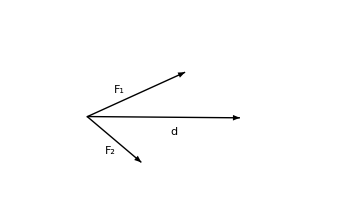

(a) What motion will result if the impressed force F_2 is doubled in magnitude?

(b) If instead the forces remain the same as originally specified but the mass of the body is halved, what will the motion of the body be (in the same unspecified time period)?

### 4. Center of Mass

(a) Sun’s mass is 2 10^30 kg. The Jupiter’s mass is 1.9 10^27kg. Jupiter is 5.2 A.U. from the Sun. Where, along the line connecting Sun and the Jupiter, does the center of mass of the Sun and Jupiter lie?
(b) Suppose the Jupiter was moving further from Sun such that after 1 year it was now at 6 A.U. During this time it goes 1/12 of the way around the Sun. Draw and describe the motion of the center of mass of Sun and the Jupiter.

Note: I deliberately put the definite article “the” in oddball places in the preceding. Feel free to ask me why.

### 5. Area Under a Curve

Consider the curve y=x^2 in the region x=0 to x=3:

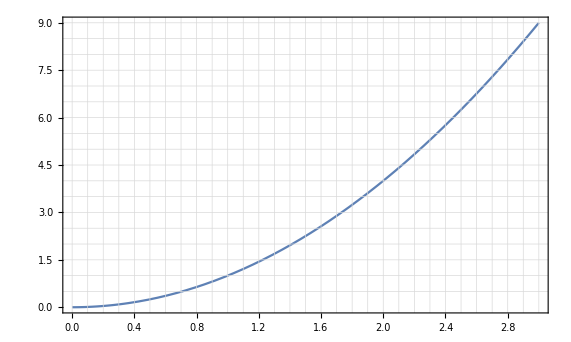

```mathematica
Plot[x^2, {x,0, 3 }, PlotRange->{{0,3},{0,9}}, GridLines->{Range[0, 3, 0.1],Range[0.5, 9, 0.5]}, GridLinesStyle->Medium, Frame->True, AspectRatio->18/30]
```

(a) What does each little square in this region represent in terms of area (in other words, what is the product of its width and height)? Count them all up. How many are there? Multiply by the individual area to get the (approximate) total area?

(b) Draw the quadrilaterals that fit under this curve. The first three or so will be impossibly scrunched, but after that it is doable. If you are not sure what I am looking for, as an example draw the quadrilateral going from x=2.0 to x=2.1 that is 4 high.

(c) Symbolically, the width 0.1 we can write as Δx. So we could have said that the quadrilateral going from x=2.0 to x=2.1, and was 4 high went from x=20Δx to  x=21Δx and was (20Δx)^2 high. So it is (Δx·(20Δx))^2 in area. If I say that was the 20th quadrilateral and let k=20, we see that its area is (k^2(Δx))^3.

So the area is the sum of (k^2(Δx))^3 from 0 to 29. Actually, be somewhat more general than that: calculate the sum of (k^2(Δx))^3 from 0 to n-1. We know n=30, but instead of plugging that in, leave it as a variable, and also replace Δx by 3/n, since if we divide the range 0 to 3 into n equal parts each of them is 3/n wide.

(d) We left n as a variable because the next thing Newton wants us to do is to take the n->∞ limit of what you found in (c). You get six terms if you multiply out the polynomial. Five of the six terms go to 0 as n->∞, so it is an easy limit to compute. Comment: your answer to (a) might not agree very well to your answer to (d). That’s because it is easy to underestimate the area in (a) due to the partial squares.